```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/00_SplinePack-034.nb"]//Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]]//Quiet;
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

C:\Users\mona_\AppData\Local\Temp\TP_ImProc_01-m101-e759f127-2f65-4f49-bf73-d838fc1c71f9.wl        22.7.2026 20:58:23.    (11295 Bytes)

```mathematica
Clear[SavitzkyGolayFilterExtended]


SavitzkyGolayFilterExtended[DOrder_,M_,nl_,nr_,data_] := Module[{i,j,p,t},
p = Table[t^i,{i,0,M}];
j = nl+nr+1;
i = Range[j];
Join[
D[Fit[Transpose[{i,Take[data,   j]}],p,t],{t,DOrder}]/.t->Take[i,  nl],
SavitzkyGolayFilter[DOrder,M,nl,nr,data],
D[Fit[Transpose[{i,Take[data,-j]}],p,t],{t,DOrder}]/.t->Take[i,-nr]]];



Clear[
ParamPadToTake,
ParamTakeToPad]


ParamPadToTake[ImgDim_,LeftRightBottomTop_] := {
{LeftRightBottomTop[[2,2]]+1,If[ListQ[ImgDim],ImgDim[[2]],-1]-LeftRightBottomTop[[2,1]]},
{LeftRightBottomTop[[1,1]]+1,If[ListQ[ImgDim],ImgDim[[1]],-1]-LeftRightBottomTop[[1,2]]}};


ParamTakeToPad[ImgDim_,RowsCols_] := Module[{LeftRightBottomTop},
LeftRightBottomTop = Reverse[RowsCols];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[1]] -= 1;
LeftRightBottomTop[[2]] = ImgDim-LeftRightBottomTop[[2]];
LeftRightBottomTop = Transpose[LeftRightBottomTop];
LeftRightBottomTop[[2]] = Reverse[LeftRightBottomTop[[2]]];
LeftRightBottomTop];



Clear[
LoadFromTIF,
SaveAsTIF]


LoadFromTIF[CheckBitLength_,fname_] := Module[{X},
X = Import[fname];
X[[-1]] = ReadQRCode[X[[-1]]];
If[
If[TrueQ[CheckBitLength],
SameQ[
Piecewise[{{1,#≤1},{8,1<#≤8}},16]&/@Ceiling[Log[2,X[[-1,1]]]],
Ceiling[Log[2,Map[Length[Union@@ImageData[#]]&,Drop[X,-1]]]]],
True],
X[[-1]] = X[[-1,2]];
Fold[
ReplacePart[#1,#2[[1]],#2[[2]]]&,
X[[-1]],
Transpose[
{Drop[X,-1],
Position[X[[-1]],Image]}]]]];


SaveAsTIF[fname_,data_] := Module[{x,X},
X = data/.x_:>MyVectorPlaceholder/;ImageQ[x];
X = Append[
Extract[data,Position[X,MyVectorPlaceholder]],
X/.MyVectorPlaceholder->Image];
X[[-1]] = {Map[Length[Union@@ImageData[#]]&,Drop[X,-1]],X[[-1]]};
X[[-1]] = WriteQRCode[X[[-1]]];
MDExport[fname,X,"ImageEncoding"->"LZW"]];



Clear[ChangeImgDims]


ChangeImgDims[
  B_?ImageQ,
nx_?IntegerQ,
ny_?IntegerQ,
padding_] := Module[{R,x,y},
{x,y} = {nx,ny}-ImageDimensions[R=B];
If[y<0,
y = {Quotient[-y,2],-y};
y = {First[y],Subtract@@y}+{1,-1};
R = ImageTake[R,y],
If[y>0,
y = {y,Quotient[y,2]};
y = {Last[y],Subtract@@y};
R = ImagePad[R,{{0,0},y},padding]]];
If[x<0,
x = {Quotient[-x,2],-x};
x = {First[x],Subtract@@x}+{1,-1};
R = ImageTake[R,All,x],
If[x>0,
x = {x,Quotient[x,2]};
x = {Last[x],Subtract@@x};
R = ImagePad[R,{x,{0,0}},padding]]];
R];
```

```mathematica
$HistoryLength = 10;
PrependTo[MyTS,FontSize->24];
DatenOrdner =OutPath= NotebookDirectory[]~~"output directory\\";
```

```mathematica
Clear[ToEnglish,Z,newID]
{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]];
newID=Map[#[[1]]->StringJoin["P",ToString@#[[2]]]&,Transpose@{Union[Drop[Z[[All,1]],2]],Table[n,{n,Length@Union[Drop[Z[[All,1]],2]]}]}];
Z[[All,1]]=Z[[All,1]]/.newID;
TableForm[Z]
Length[Z]
```

Proband | Instrument | Task | Begin (s) | End (s) | Emission rate (P/s) | ER σ (P/s) | Water emission (mg/s) | Particles/Water (P/mg)
 |  |  |  |  |  |  |  | 
P1 | C | Breathing | 6206 | 7408 | -98 | 171 | 6.35133 | -15.4298
P1 | C | Playing | 1200 | 2408 | 355 | 261 | 19.6555 | 18.0611
P1 | C | Playing With Surgical Mask | 8449 | 9061 | 790 | 764 | 7.36465 | 107.269
P1 | C | Speaking | 4010 | 5236 | 22 | 100 | 8.70055 | 2.52858
P32 | S | Breathing | 3340 | 4555 | 228 | 153 |  | 
P32 | S | Speaking | 1200 | 2405 | 89 | 94 |  | 
P32 | S | Speaking With Surgical Mask | 5466 | 6682 | -122 | 196 |  | 
P36 | S | Speaking With Surgical Mask | 4524 | 5723 | -1 | 184 | 4.8826 | -0.204809
P37 | S | Breathing | 4051 | 5256 | -157 | 302 | 8.03068 | -19.55
P37 | S | Speaking | 7443 | 8659 | 590 | 162 | 5.92732 | 99.5391
P37 | S | Speaking With Surgical Mask | 1200 | 2408 | 666 | 215 | 5.7454 | 115.919
P38 | S | Speaking | 5299 | 6523 | -137 | 198 | 5.18286 | -26.4333
P38 | S | Speaking With Surgical Mask | 424 | 1648 | 78 | 93 | 6.08984 | 12.8082
P39 | S | Speaking With Surgical Mask | 876 | 2098 | -50 | 107 | 5.95228 | -8.40014
P40 | S | Breathing | 4106 | 5320 | -199 | 335 | 8.3125 | -23.9398
P40 | S | Speaking | 1869 | 3080 | 16 | 189 | 17.5803 | 0.910107
P40 | S | Speaking With Surgical Mask | 6825 | 8040 | 114 | 267 | 5.6046 | 20.3404
P41 | S | Breathing | 3261 | 4466 | -105 | 151 | 3.11025 | -33.7593
P41 | S | Speaking | 5840 | 7058 | -260 | 312 | 5.79921 | -44.8337
P41 | S | Speaking With Surgical Mask | 1200 | 2405 | 473 | 83 | 6.94787 | 68.0784
P42 | S | Breathing | 3646 | 4851 | 48 | 164 | 3.95646 | 12.1321
P42 | S | Speaking | 7694 | 8906 | 203 | 327 | 4.58863 | 44.2398
P42 | S | Speaking With Surgical Mask | 1200 | 2440 | -163 | 249 | 9.10583 | -17.9006
P43 | S | Breathing | 3656 | 4859 | 455 | 302 | 8.05346 | 56.4975
P43 | S | Speaking | 7093 | 8303 | 1605 | 305 | 8.3908 | 191.281
P43 | S | Speaking With Surgical Mask | 1200 | 2403 | 586 | 610 | 10.1777 | 57.5767
P33 | S | Breathing | 4239 | 5441 | 296 | 224 | 8.28801 | 35.7142
P33 | S | Playing | 10644 | 11848 | 2122 | 605 | 12.8713 | 164.863
P33 | S | Speaking | 7057 | 8273 | 242 | 209 | 8.4451 | 28.6557
P33 | S | Speaking With Surgical Mask | 1200 | 2408 | 947 | 475 | 18.7504 | 50.5057
P34 | S | Breathing | 3418 | 4622 | 559 | 443 | 9.5607 | 58.4685
P34 | S | Speaking | 5828 | 7040 | 1671 | 207 | 9.96255 | 167.728
P34 | S | Speaking With Surgical Mask | 944 | 2159 | 2 | 413 | 9.34569 | 0.214002
P35 | S | Breathing | 4027 | 5230 | -44 | 210 | 12.5258 | -3.51274
P35 | S | Playing | 10374 | 11579 | 1355 | 428 | 16.1923 | 83.682
P35 | S | Speaking | 7275 | 8480 | 481 | 229 | 8.78184 | 54.7721
P35 | S | Speaking With Surgical Mask | 1093 | 2317 | 970 | 160 | 16.4966 | 58.8001
P24 | O | Breathing | 6157 | 7360 | -48 | 198 | 5.04529 | -9.51383
P24 | O | Playing | 1828 | 3032 | 838 | 288 | 19.4271 | 43.1356
P24 | O | Playing With Surgical Mask | 8546 | 9159 | 320 | 568 | 8.02528 | 39.874
P24 | O | Speaking | 4113 | 5328 | -245 | 356 | 8.90999 | -27.4972
P25 | O | Breathing | 5900 | 7104 | 23 | 166 | 5.18188 | 4.43854
P25 | O | Playing | 1200 | 2400 | 466 | 115 | 21.9253 | 21.254
P25 | O | Playing With Surgical Mask | 8292 | 8912 | 215 | 400 | 9.70404 | 22.1557
P25 | O | Speaking | 3515 | 4735 | 56 | 307 | 8.71046 | 6.42905
P25 | O | Speaking With Surgical Mask | 10570 | 11789 | -164 | 273 | 4.28641 | -38.2605
P26 | O | Breathing | 6226 | 7429 | 93 | 95 | 5.80198 | 16.029
P26 | O | Playing | 1200 | 2427 | 1309 | 210 | 16.382 | 79.9047
P26 | O | Playing With Surgical Mask | 8482 | 9086 | 911 | 612 | 6.44717 | 141.302
P26 | O | Speaking | 3697 | 4929 | 189 | 114 | 6.88974 | 27.4321
P26 | O | Speaking With Surgical Mask | 10224 | 11456 | -66 | 142 | 4.88131 | -13.521
P27 | O | Speaking | 3109 | 4303 | -164 | 319 | 11.3842 | -14.4059
P28 | O | Breathing | 6070 | 7281 | 117 | 304 | 9.31335 | 12.5626
P28 | O | Playing | 1200 | 2429 | 521 | 316 | 35.627 | 14.6238
P28 | O | Playing With Surgical Mask | 8842 | 9451 | 1610 | 483 | 9.25584 | 173.944
P28 | O | Speaking | 3683 | 4905 | 257 | 227 | 14.3611 | 17.8955
P29 | O | Breathing | 6229 | 7432 | 181 | 223 | 9.50645 | 19.0397
P29 | O | Playing | 1200 | 2433 | 2535 | 195 | 34.9787 | 72.4727
P29 | O | Playing With Surgical Mask | 8409 | 9017 | 670 | 238 | 13.4193 | 49.9282
P29 | O | Speaking | 3689 | 4894 | 715 | 296 | 18.8318 | 37.9676
P30 | O | Breathing | 7834 | 9039 | -187 | 432 | 7.19722 | -25.9823
P30 | O | Playing | 1569 | 2777 | 1229 | 147 | 32.4661 | 37.8549
P30 | O | Playing With Surgical Mask | 10204 | 10835 | 1053 | 273 | 15.7934 | 66.6734
P30 | O | Speaking | 5280 | 6512 | -175 | 294 | 9.94692 | -17.5934
P31 | O | Breathing | 6075 | 7278 | -145 | 266 | 5.34168 | -27.145
P31 | O | Playing | 1200 | 2404 | 1645 | 461 | 22.9649 | 71.6312
P31 | O | Playing With Surgical Mask | 8431 | 9042 | 1589 | 534 | 14.8384 | 107.087
P31 | O | Speaking | 4015 | 5222 | 9 | 191 | 7.94626 | 1.13261
P21 | O | Playing | 1200 | 2402 | 218 | 185 | 17.797 | 12.2493
P21 | O | Playing With Surgical Mask | 8608 | 9211 | -209 | 268 | 17.5343 | -11.9195
P21 | O | Speaking | 3747 | 4961 | -3 | 148 | 11.8492 | -0.253182
P21 | O | Speaking With Surgical Mask | 10242 | 11447 | -136 | 279 | 10.1543 | -13.3933
P22 | O | Breathing | 5645 | 6848 | 21 | 244 | 7.20408 | 2.91501
P22 | O | Playing | 1032 | 2258 | 1484 | 211 | 26.5107 | 55.9774
P22 | O | Playing With Surgical Mask | 8124 | 8741 | 1263 | 1224 | 10.8125 | 116.809
P22 | O | Speaking | 3379 | 4595 | 144 | 409 | 13.1723 | 10.932
P23 | O | Breathing | 6274 | 7483 | -150 | 196 | 8.32992 | -18.0074
P23 | O | Playing | 1200 | 2411 | 660 | 274 | 24.5285 | 26.9075
P23 | O | Playing With Surgical Mask | 8782 | 9386 | 894 | 620 | 14.5733 | 61.3453
P23 | O | Speaking | 3565 | 4770 | 725 | 128 | 12.7055 | 57.0621
P2 | F | Breathing | 5183 | 6376 | 48 | 35 | 6.17609 | 7.7719
P2 | F | Playing | 1200 | 2392 | 1434 | 366 | 26.468 | 54.1787
P2 | F | Speaking | 3057 | 4260 | 641 | 384 | 11.7497 | 54.5544
P2 | F | Speaking With Surgical Mask | 6929 | 8125 | 447 | 189 | 8.23895 | 54.2545
P13 | F | Breathing | 6063 | 7278 | 119 | 151 | 7.49066 | 15.8865
P13 | F | Playing | 1379 | 2586 | 343 | 486 | 29.3035 | 11.7051
P13 | F | Speaking | 3612 | 4826 | 63 | 92 | 14.9865 | 4.20379
P15 | F | Breathing | 3293 | 4493 | 39 | 213 |  | 
P15 | F | Playing | 1588 | 2755 | 57 | 175 |  | 
P15 | F | Speaking | 4983 | 6228 | -144 | 175 |  | 
P15 | F | Speaking With Surgical Mask | 7425 | 8615 | 455 | 293 |  | 
P16 | F | Breathing | 5604 | 6813 | -2 | 317 | 8.18271 | -0.244418
P16 | F | Playing | 1200 | 2405 | 2318 | 644 | 27.4037 | 84.587
P16 | F | Speaking | 3543 | 4759 | -79 | 366 | 13.6893 | -5.77093
P16 | F | Speaking With Surgical Mask | 7928 | 9141 | 432 | 245 | 6.09656 | 70.8597
P17 | F | Playing | 1200 | 2401 | 1143 | 206 | 21.095 | 54.1834
P17 | F | Speaking | 4001 | 5223 | -80 | 174 | 6.67978 | -11.9764
P17 | F | Speaking With Surgical Mask | 8298 | 9499 | -89 | 291 | 5.70864 | -15.5904
P18 | F | Breathing | 4996 | 6211 | 350 | 175 | 12.8319 | 27.2759
P18 | F | Playing | 1200 | 2416 | 635 | 128 |  | 
P18 | F | Speaking | 3159 | 4364 | 7 | 67 | 23.5479 | 0.297266
P19 | F | Breathing | 5401 | 6604 | -1 | 79 |  | 
P19 | F | Playing | 1200 | 2420 | 1171 | 176 |  | 
P19 | F | Speaking | 3399 | 4611 | 129 | 256 |  | 
P19 | F | Speaking With Surgical Mask | 7200 | 8407 | 486 | 220 |  | 
P20 | F | Breathing | 5911 | 7119 | 274 | 317 | 4.31308 | 63.5277
P20 | F | Playing | 1200 | 2404 | 799 | 307 | 8.14177 | 98.1359
P20 | F | Speaking | 3521 | 4759 | -121 | 140 | 5.55579 | -21.7791
P20 | F | Speaking With Surgical Mask | 8075 | 9283 | 474 | 368 | 5.38106 | 88.0868
P3 | F | Playing | 1200 | 2398 | 11 | 288 |  | 
P3 | F | Speaking | 3145 | 4340 | 5 | 203 | 18.3802 | 0.272032
P3 | F | Speaking With Surgical Mask | 6889 | 8093 | 943 | 173 | 5.75107 | 163.97
P4 | F | Breathing | 5914 | 7118 | 149 | 368 | 3.98727 | 37.3689
P4 | F | Playing | 1200 | 2413 | 15 | 313 | 18.7977 | 0.797972
P5 | F | Breathing | 5897 | 7103 | -127 | 237 | 6.85545 | -18.5254
P5 | F | Playing | 1160 | 2375 | 1708 | 348 | 29.6123 | 57.6787
P5 | F | Speaking | 3754 | 4965 | 251 | 163 | 10.3012 | 24.3661
P5 | F | Speaking With Surgical Mask | 8233 | 9443 | 564 | 295 | 6.65816 | 84.7081
P6 | F | Playing | 1095 | 2307 | 905 | 75 | 12.3282 | 73.409
P6 | F | Speaking | 3354 | 4557 | 228 | 191 | 9.82398 | 23.2085
P6 | F | Speaking With Surgical Mask | 8378 | 9576 | 88 | 239 | 5.65073 | 15.5732
P7 | F | Breathing | 6529 | 7740 | 181 | 209 | 3.6099 | 50.14
P7 | F | Playing | 1200 | 2425 | 700 | 368 | 13.7627 | 50.862
P7 | F | Speaking | 3939 | 5168 | 64 | 253 | 7.93103 | 8.06957
P8 | F | Breathing | 6108 | 7316 | -11 | 196 | 4.08124 | -2.69526
P8 | F | Playing | 1200 | 2404 | 2358 | 120 | 24.8061 | 95.0573
P8 | F | Speaking | 3849 | 5063 | 233 | 215 | 9.1381 | 25.4976
P8 | F | Speaking With Surgical Mask | 8331 | 9540 | 31 | 316 | 4.55566 | 6.80472
P9 | F | Breathing | 6620 | 7824 | 200 | 83 | 6.77415 | 29.524
P9 | F | Playing | 1200 | 2409 | 364 | 278 | 33.7478 | 10.7859
P9 | F | Speaking | 4532 | 5738 | 298 | 187 | 12.2373 | 24.3518
P10 | F | Breathing | 6635 | 7852 | 21 | 124 | 3.95503 | 5.3097
P10 | F | Playing | 1200 | 2418 | 512 | 294 | 17.1398 | 29.872
P10 | F | Speaking | 4614 | 5820 | 410 | 161 | 6.47669 | 63.3039
P10 | F | Speaking With Surgical Mask | 9133 | 10355 | 1125 | 161 | 4.30338 | 261.423
P11 | F | Breathing | 6927 | 8129 | 86 | 191 | 5.96245 | 14.4236
P11 | F | Playing | 1516 | 2727 | 390 | 155 | 19.7321 | 19.7648
P11 | F | Speaking | 4058 | 5259 | 427 | 123 | 11.2176 | 38.0651
P11 | F | Speaking With Surgical Mask | 9464 | 10668 | 513 | 395 | 8.31043 | 61.7296
P12 | F | Breathing | 6116 | 7321 | 589 | 354 | 5.46943 | 107.689
P12 | F | Playing | 1200 | 2423 | 1917 | 365 | 8.88526 | 215.751
P12 | F | Speaking | 3664 | 4888 | 681 | 151 | 2.84054 | 239.743
P12 | F | Speaking With Surgical Mask | 9035 | 10245 | 776 | 531 | 3.76071 | 206.344
P14 | F | Breathing | 6432 | 7665 | 204 | 140 | 3.8381 | 53.1514
P14 | F | Playing | 1200 | 2403 | 1410 | 342 | 13.9815 | 100.848
P14 | F | Speaking | 3807 | 5022 | 770 | 152 | 5.98523 | 128.65
P14 | F | Speaking With Surgical Mask | 8636 | 9874 | 559 | 162 | 5.27915 | 105.888
P44 | T | Playing | 1200 | 2415 | 192 | 448 | 30.0835 | 6.38223
P44 | T | Playing With Surgical Mask | 8984 | 9589 | 28 | 2562 | 9.06738 | 3.08799
P44 | T | Speaking | 3907 | 5135 | -306 | 348 | 13.4608 | -22.7327

152

```mathematica
Entries[Z,"Instrument"]
```

{{67,F},{43,O},{33,S},{4,C},{3,T}}

```mathematica
Entries[Z,"Aufgabe"/.ToEnglish]
```

{{41,Speaking},{35,Breathing},{33,Playing},{29,Speaking With Surgical Mask},{12,Playing With Surgical Mask}}

```mathematica
Measurements = {"Atmen","Sprechen mit MNS","Sprechen"}/.ToEnglish;
TableForm[Subsets[Measurements,{2}]]
OutPath = StringJoin[OutPath~~"\\Fig\\"]
```

Breathing | Speaking With Surgical Mask
Breathing | Speaking
Speaking With Surgical Mask | Speaking

C:\Users\mona_\Downloads\upload aerosol study 2020\output directory\\Fig\

```mathematica
Clear[R,TaskPlot,
A,h,i]

R = {-600*0,3000+200};

TaskPlot[task_?StringQ] := Module[{A,h,i},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Instrument","Emissionsrate (P/s)","ER σ (P/s)","Proband"}/.ToEnglish],2];
Rest/@A
]

TaskPlot[{"Sprechen","Sprechen"}[[2]]/.ToEnglish]
```

{{22,100,P1},{89,94,P32},{590,162,P37},{-137,198,P38},{16,189,P40},{-260,312,P41},{203,327,P42},{1605,305,P43},{242,209,P33},{1671,207,P34},{481,229,P35},{-245,356,P24},{56,307,P25},{189,114,P26},{-164,319,P27},{257,227,P28},{715,296,P29},{-175,294,P30},{9,191,P31},{-3,148,P21},{144,409,P22},{725,128,P23},{641,384,P2},{63,92,P13},{-144,175,P15},{-79,366,P16},{-80,174,P17},{7,67,P18},{129,256,P19},{-121,140,P20},{5,203,P3},{251,163,P5},{228,191,P6},{64,253,P7},{233,215,P8},{298,187,P9},{410,161,P10},{427,123,P11},{681,151,P12},{770,152,P14},{-306,348,P44}}

```mathematica
{{"C","F","O","S","T"},{{{22,100,"P1"}},{{-144,175,"P15"},{-121,140,"P20"},{-80,174,"P17"},{-79,366,"P16"},{5,203,"P3"},{7,67,"P18"},{63,92,"P13"},{64,253,"P7"},{129,256,"P19"},{228,191,"P6"},{233,215,"P8"},{251,163,"P5"},{298,187,"P9"},{410,161,"P10"},{427,123,"P11"},{641,384,"P2"},{681,151,"P12"},{770,152,"P14"}},{{-245,356,"P24"},{-175,294,"P30"},{-164,319,"P27"},{-3,148,"P21"},{9,191,"P31"},{56,307,"P25"},{144,409,"P22"},{189,114,"P26"},{257,227,"P28"},{715,296,"P29"},{725,128,"P23"}},{{-260,312,"P41"},{-137,198,"P38"},{16,189,"P40"},{89,94,"P32"},{203,327,"P42"},{242,209,"P33"},{481,229,"P35"},{590,162,"P37"},{1605,305,"P43"},{1671,207,"P34"}},{{-306,348,"P44"}}}};
```

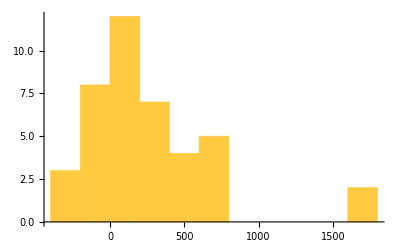

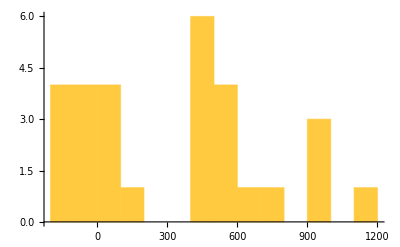

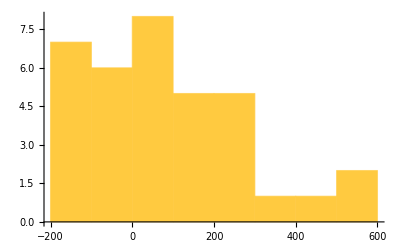

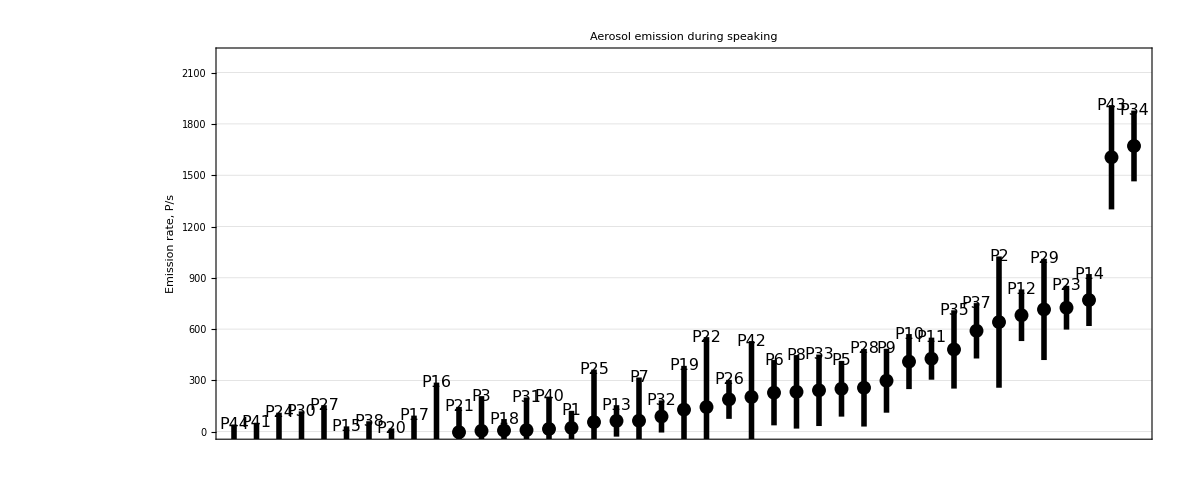
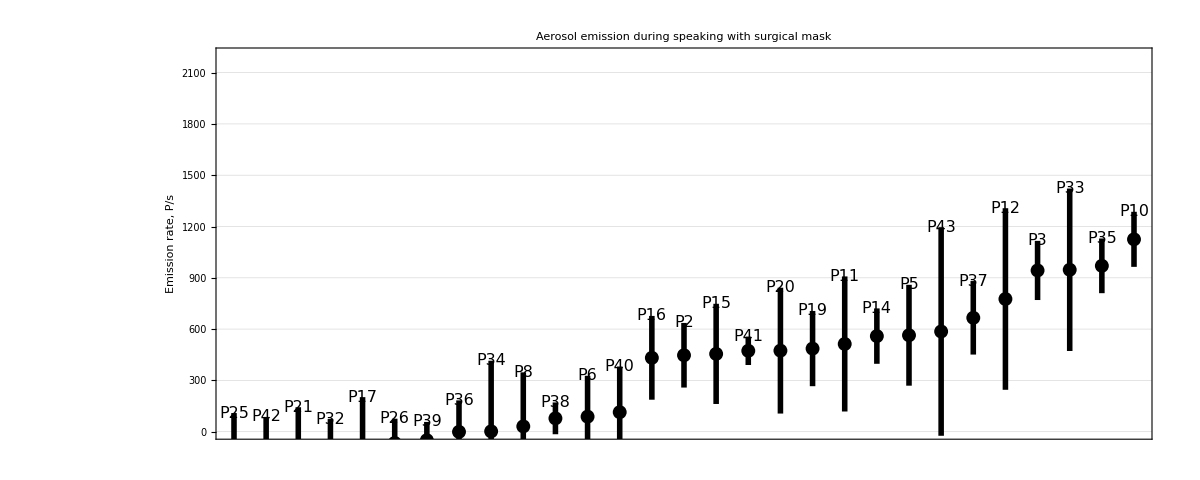
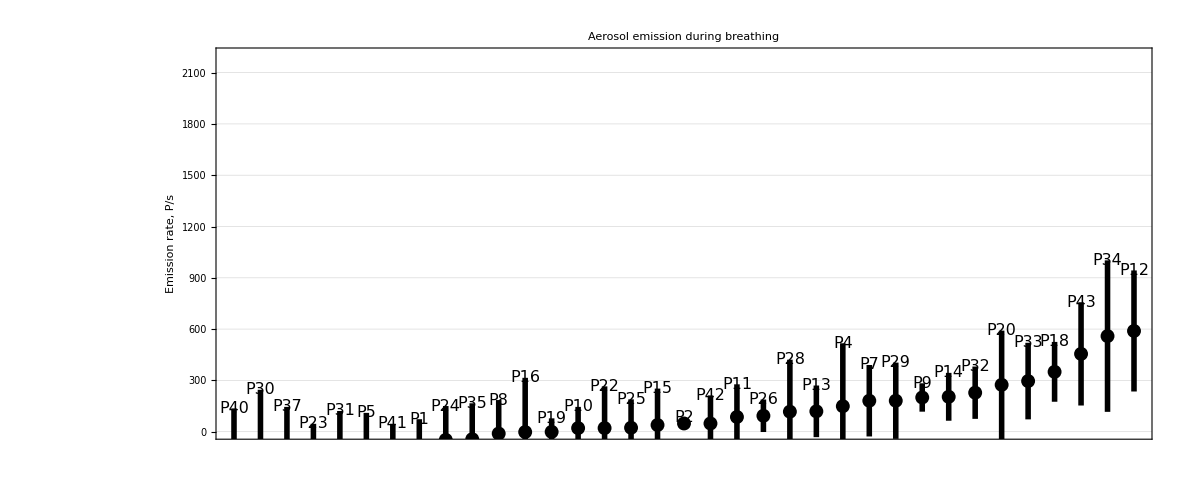
{{Null,-Graphics-},{Null,-Graphics-},{Null,-Graphics-}}

```mathematica
Clear[R,TaskPlot,
A,h,i]

R = {-600*0,2000+200};

TaskPlot[task_?StringQ] := Module[{D,A,h,i,G,H},
A = SelectRows[Z,"Aufgabe"/.ToEnglish,(#==task)&];
If[Length[A]==2,Return[1]];
A = Drop[ExtractColumn[A,{"Emissionsrate (P/s)","ER σ (P/s)","Proband"}/.ToEnglish],2];
A=SortBy[A,First];
i=0;
D=Flatten@Map[(++i;
{Point[{i,#[[1]]}],Line[h={{i,Max[-Infinity,#[[1]]-#[[2]]]},{i,#[[1]]+#[[2]]}}],Text@@Prepend[If[MemberQ[{(*"Playing"*)},task],{h[[1]],{0,2}},{h[[2]],{0,-2}}],Style[StringDrop[#[[3]],0],FontColor->GrayLevel[0],FontFamily->"Arial",FontSlant->"Plain",FontWeight->"Plain",FontSize->Round[(FontSize/. MyTS)*2/3]]]})&,A];
G=Graphics[{AbsoluteThickness[4],AbsolutePointSize[10],D},AspectRatio->0.4,Axes->False,DisplayFunction->Identity,Frame->True,FrameLabel->{None,"Emission rate,  P/s"/. ToEnglish},FrameTicks->{None,Automatic},GridLines->{None,Automatic},ImageSize->1200,LabelStyle->MyTS,PlotLabel->StringJoin["Aerosol emission during ",ToLowerCase[task]],PlotRange->{All,R},PlotRangeClipping->True];
Export[OutPath~~StringJoin["Aerosol emission during ",ToLowerCase[task]]~~".tif",G];
H= Histogram[First/@A,10];
{H,G}
];



{TaskPlot[{"Sprechen","Sprechen"}[[2]]/.ToEnglish],TaskPlot[{"Sprechen mit MNS","Sprechen mit MNS"}[[2]]/.ToEnglish],TaskPlot[{"Atmen","Atmen"}[[2]]/.ToEnglish]}
```